CODE DOCUMENTATION

File: Theory/FFL/AND.nb
Paper: An information-theoretic perspective on feed-forward loop abundances in transcriptional networks
Authors: Mintu Nandi, Sudip Chattopadhyay, and Suman K Banik
Contact: mintunandi@ubi.s.u-tokyo.ac.jp; sudip@chem.iiests.ac.in; skbanik@jcbose.ac.in

Purpose
Evaluates the analytical fluctuation decomposition, total mutual information, pathway mutual information, interference mutual information, pathway-interference strength, and local pathway sensitivities for all FFL motifs and both organisms under the AND gate.

How to run
Open the notebook in Wolfram Mathematica and evaluate the input cells.

Inputs and outputs
No external input files are required. Parameter values and analytical expressions are embedded in the notebook. Results are returned as evaluated cells, printed tables, and plots.

Code-to-manuscript notation
xav, yav, zav -> <x>, <y>, <z>; Kxy, Kxz, Kyz -> K_XY, K_XZ, K_YZ; fyxp, fzxp, fzyp -> f'_YX, f'_ZX, f'_ZY; eta xz1, eta xz2 -> zeta_XZ,d, zeta_XZ,ind; eta zi, eta zd, eta zind, eta zsyn, eta p -> eta_Z,0^2, eta_Z,d^2, eta_Z,ind^2, eta_Z,int^2, eta_Z,path^2; Ixz -> I(X;Z); Ixz0 -> I_path(X;Z); Ixzs -> I_int(X;Z); Df -> S_XZ; Ed and Ei -> direct- and indirect-path logarithmic sensitivities.

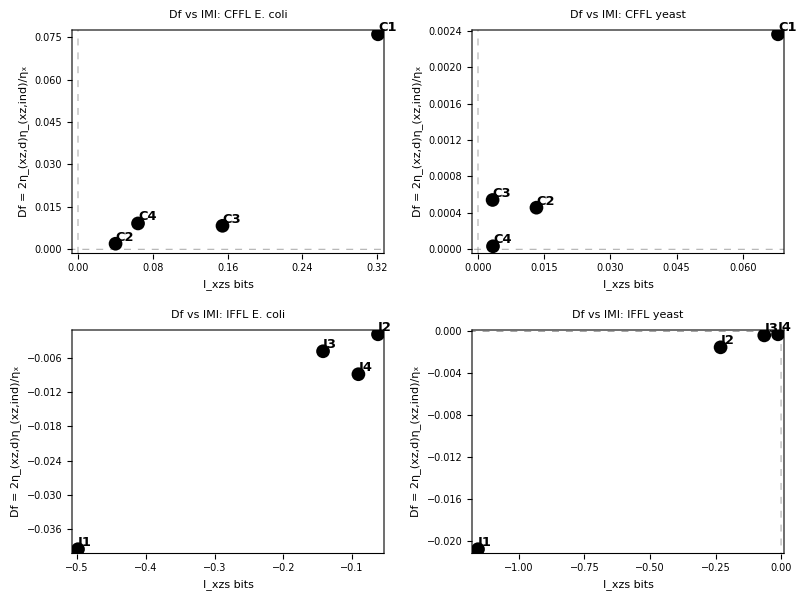

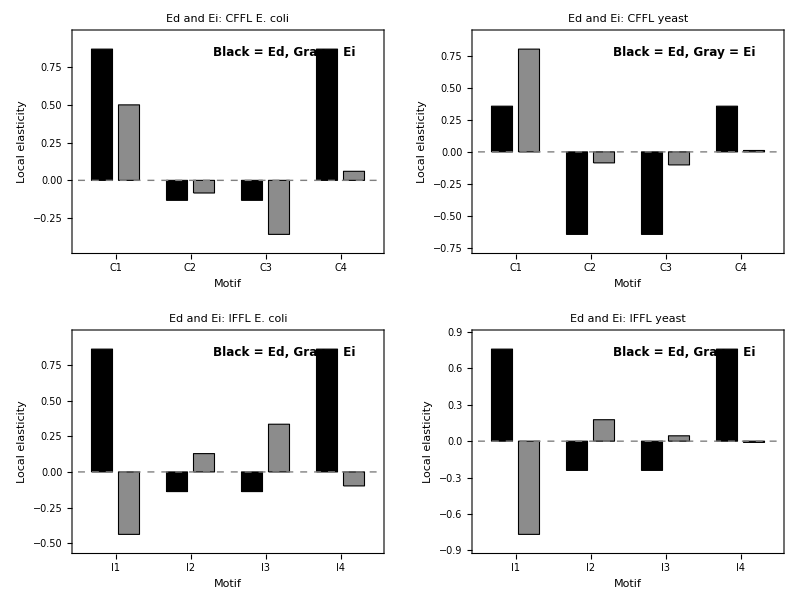

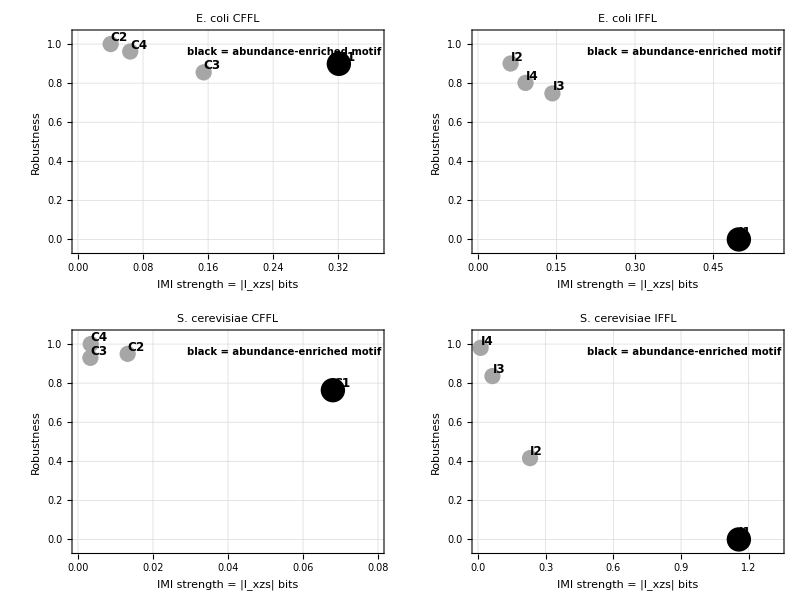

Class | Motif | Ixzs | AbsIxzs | MeanAbsLogSensitivity | Robustness
Ecoli CFFL | C1 | 0.320838 | 0.320838 | 0.023087 | 0.898774
Ecoli CFFL | C2 | 0.0401676 | 0.0401676 | 0.013282 | 1.
Ecoli CFFL | C3 | 0.154543 | 0.154543 | 0.0273075 | 0.855202
Ecoli CFFL | C4 | 0.0642 | 0.0642 | 0.016986 | 0.961761
Ecoli IFFL | I1 | -0.498485 | 0.498485 | 0.110145 | 0.
Ecoli IFFL | I2 | -0.0622993 | 0.0622993 | 0.0229207 | 0.900491
Ecoli IFFL | I3 | -0.142206 | 0.142206 | 0.0377476 | 0.74742
Ecoli IFFL | I4 | -0.0907801 | 0.0907801 | 0.0325314 | 0.801271
Yeast CFFL | C1 | 0.0679715 | 0.0679715 | 0.0260234 | 0.763874
Yeast CFFL | C2 | 0.0132448 | 0.0132448 | 0.00782354 | 0.950059
Yeast CFFL | C3 | 0.00330802 | 0.00330802 | 0.00983689 | 0.929463
Yeast CFFL | C4 | 0.00339635 | 0.00339635 | 0.00294173 | 1.
Yeast IFFL | I1 | -1.1564 | 1.1564 | 0.100693 | 0.
Yeast IFFL | I2 | -0.230692 | 0.230692 | 0.0600146 | 0.416145
Yeast IFFL | I3 | -0.0640172 | 0.0640172 | 0.0189705 | 0.836026
Yeast IFFL | I4 | -0.0115971 | 0.0115971 | 0.0048257 | 0.980727

Export completed. Files saved in: F:\Colab\FFL-Info-Decomp\Theory\Data_exports_AND

```mathematica
(*
Notations: xav=<x>, yav=<y>, zav=<z>
		fijp=Subscript[f, ij]'
*)
(*------Squared coefficient of variation: Subscript[CV^2, i]=Subscript[σ^2, i]/(<i>^2), Subscript[CV^2, ij]=Subscript[σ^2, ij]/(<i><j>)------*)

Γxy=1/(βx+βy);
Γxz=1/(βx+βz);
Γyz=1/(βy+βz);
Γxyz1=1/((βx+βy)*(βx+βz));
Γxyz2=(βx+βy+βz)/(βy*(βx+βy)*(βx+βz)*(βy+βz));
Γxyz3=(2*βx+βy+βz)/((βx+βy)*(βx+βz)*(βy+βz));



ηxy=Γxy/yav*fyxp; (*Subscript[η^2, xy]*)

ηxz1=Γxz/zav*fzxp; (*Subscript[η^2, xz,d]*)
ηxz2=Γxyz1/zav*fyxp*fzyp; (*Subscript[η^2, xz,ind]*)

ηxz=ηxz1+ηxz2; (*Subscript[η^2, xz]*)

ηyz1=Γyz/zav*fzyp; (*Subscript[η^2, yz,Subscript[ind, 1]]*)
ηyz2=(Γxyz2*xav)/(yav*zav)*fyxp^2*fzyp; (*Subscript[η^2, yz,Subscript[ind, 2]]*)
ηyz3=(Γxyz3*xav)/(yav*zav)*fyxp*fzxp; (*Subscript[η^2, yz,cross]*)
ηyz=ηyz1+ηyz2+ηyz3; (*Subscript[η^2, yz]*)


ηx=1/xav;

ηy=1/yav+(fyxp^2*xav)/(βy*yav)*ηxy;

ηzi=1/zav; (*Subscript[η^2, z,int]*)

ηzd=(fzxp*xav)/(βz*zav)*ηxz1; (*Subscript[η^2, z,d]*)

ηzind=(fzyp*yav)/(βz*zav)*(ηyz1+ηyz2); (*Subscript[η^2, z,ind]*)

prefactor1=(fzxp*xav)/(βz*zav);
ηzsyn1=prefactor1*ηxz2; 
prefactor2=(fzyp*yav)/(βz*zav);
ηzsyn2=prefactor2*ηyz3; 
ηzsyn=ηzsyn1+ηzsyn2; (*Subscript[η^2, z,cross]*)

ηp=ηzi+ηzd+ηzind; (*Subscript[η^2, z,path]*)

ηz=ηp+ηzsyn; (*Subscript[η^2, z]*)

ηr=ηzsyn/ηp; (*Relative synergy noise*)


(*Entropy Gain*)
Hz=1/2*Log2[2*Pi*Exp[1]*zav^2*ηz];

Hz0=1/2*Log2[2*Pi*Exp[1]*zav^2*ηp];
Hzs=1/2*Log2[1+ηzsyn/ηp];


(** Information XY->Z **)

Ixz=1/2*Log2[(ηx*ηz)/(ηx*ηz-ηxz^2)];

Ixz0=1/2*Log2[ηp/(ηp-(ηxz1^2+ηxz2^2)/ηx)];
Ixzs=1/2*Log2[(1+ηzsyn/ηp)/(1+(ηzsyn-(2*ηxz1*ηxz2)/ηx)/(ηp-(ηxz1^2+ηxz2^2)/ηx))];



Df=(2*ηxz1*ηxz2)/ηx;

Eyx =(xav*fyxpp)/fyx;
Ezx =(xav*fzxpp)/fzx;
Ezy =(yav*fzypp)/fzy;
Ed=Ezx;
Ei=Eyx*Ezy;

(*------Particular motifs and their functions------*)


(*##################################################*)

(*C1FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0007*10^-3; βy=9.9884*10^-2; βz=4.9986*10^-1;
xav=10.64; yav=13.17; zav=99.94;
Kxy=63.52; Kxz=69.95; Kyz=18.40;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipc1ae=Ixz0;
Isc1ae=Ixzs; 
Dc1ae=Df;
Edc1ae=Ed;
Eic1ae=Ei;

(*C2FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0007*10^-3; βy=9.9884*10^-2; βz=4.9986*10^-1;
xav=10.64; yav=13.17; zav=99.94;
Kxy=63.52; Kxz=69.95; Kyz=18.40;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipc2ae=Ixz0;
Isc2ae=Ixzs; 
Dc2ae=Df;
Edc2ae=Ed;
Eic2ae=Ei;

(*C3FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0007*10^-3; βy=9.9884*10^-2; βz=4.9986*10^-1;
xav=10.64; yav=13.17; zav=99.94;
Kxy=63.52; Kxz=69.95; Kyz=18.40;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;


Ipc3ae=Ixz0;
Isc3ae=Ixzs; 
Dc3ae=Df;
Edc3ae=Ed;
Eic3ae=Ei;

(*C4FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0007*10^-3; βy=9.9884*10^-2; βz=4.9986*10^-1;
xav=10.64; yav=13.17; zav=99.94;
Kxy=63.52; Kxz=69.95; Kyz=18.40;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;


Ipc4ae=Ixz0;
Isc4ae=Ixzs; 
Dc4ae=Df;
Edc4ae=Ed;
Eic4ae=Ei;


(*##################################################*)


(*C1FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=12.336*10^-3; βy=0.9040*10^-2; βz=0.2863*10^-1;
xav=50.00; yav=63.42; zav=499.96;
Kxy=467.23; Kxz=27.69; Kyz=499.80;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;


Ipc1ay=Ixz0;
Isc1ay=Ixzs; 
Dc1ay=Df;
Edc1ay=Ed;
Eic1ay=Ei;

(*C2FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=12.336*10^-3; βy=0.9040*10^-2; βz=0.2863*10^-1;
xav=50.00; yav=63.42; zav=499.96;
Kxy=467.23; Kxz=27.69; Kyz=499.80;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipc2ay=Ixz0;
Isc2ay=Ixzs; 
Dc2ay=Df;
Edc2ay=Ed;
Eic2ay=Ei;

(*C3FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=12.336*10^-3; βy=0.9040*10^-2; βz=0.2863*10^-1;
xav=50.00; yav=63.42; zav=499.96;
Kxy=467.23; Kxz=27.69; Kyz=499.80;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Ipc3ay=Ixz0;
Isc3ay=Ixzs; 
Dc3ay=Df;
Edc3ay=Ed;
Eic3ay=Ei;

(*C4FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=12.336*10^-3; βy=0.9040*10^-2; βz=0.2863*10^-1;
xav=50.00; yav=63.42; zav=499.96;
Kxy=467.23; Kxz=27.69; Kyz=499.80;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Ipc4ay=Ixz0;
Isc4ay=Ixzs; 
Dc4ay=Df;
Edc4ay=Ed;
Eic4ay=Ei;

(*##################################################*)

(*I1FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0023*10^-3; βy=9.8712*10^-2; βz=0.7257*10^-1;
xav=15.93; yav=48.82; zav=56.96;
Kxy=54.32; Kxz=99.55; Kyz=37.29;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Ipi1ae=Ixz0;
Isi1ae=Ixzs; 
Di1ae=Df;
Edi1ae=Ed;
Eii1ae=Ei;

(*I2FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0023*10^-3; βy=9.8712*10^-2; βz=0.7257*10^-1;
xav=15.93; yav=48.82; zav=56.96;
Kxy=54.32; Kxz=99.55; Kyz=37.29;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Ipi2ae=Ixz0;
Isi2ae=Ixzs; 
Di2ae=Df;
Edi2ae=Ed;
Eii2ae=Ei;

(*I3FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0023*10^-3; βy=9.8712*10^-2; βz=0.7257*10^-1;
xav=15.93; yav=48.82; zav=56.96;
Kxy=54.32; Kxz=99.55; Kyz=37.29;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipi3ae=Ixz0;
Isi3ae=Ixzs; 
Di3ae=Df;
Edi3ae=Ed;
Eii3ae=Ei;


(*I4FFL-AND-Ecoli*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=5.0023*10^-3; βy=9.8712*10^-2; βz=0.7257*10^-1;
xav=15.93; yav=48.82; zav=56.96;
Kxy=54.32; Kxz=99.55; Kyz=37.29;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipi4ae=Ixz0;
Isi4ae=Ixzs; 
Di4ae=Df;
Edi4ae=Ed;
Eii4ae=Ei;


(*##################################################*)


(*I1FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=1.2494*10^-3; βy=6.2408*10^-2; βz=0.2536*10^-1;
xav=50.01; yav=446.66; zav=306.79;
Kxy=217.30; Kxz=157.60; Kyz=25.69;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Ipi1ay=Ixz0;
Isi1ay=Ixzs; 
Di1ay=Df;
Edi1ay=Ed;
Eii1ay=Ei;
Ei1ay=EE;

(*I2FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=1.2494*10^-3; βy=6.2408*10^-2; βz=0.2536*10^-1;
xav=50.01; yav=446.66; zav=306.79;
Kxy=217.30; Kxz=157.60; Kyz=25.69;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Ipi2ay=Ixz0;
Isi2ay=Ixzs; 
Di2ay=Df;
Edi2ay=Ed;
Eii2ay=Ei;

(*I3FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=1.2494*10^-3; βy=6.2408*10^-2; βz=0.2536*10^-1;
xav=50.01; yav=446.66; zav=306.79;
Kxy=217.30; Kxz=157.60; Kyz=25.69;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*-Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipi3ay=Ixz0;
Isi3ay=Ixzs; 
Di3ay=Df;
Edi3ay=Ed;
Eii3ay=Ei;


(*I4FFL-AND-Yeast*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=1.2494*10^-3; βy=6.2408*10^-2; βz=0.2536*10^-1;
xav=50.01; yav=446.66; zav=306.79;
Kxy=217.30; Kxz=157.60; Kyz=25.69;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=Kxy/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Ipi4ay=Ixz0;
Isi4ay=Ixzs; 
Di4ay=Df;
Edi4ay=Ed;
Eii4ay=Ei;


(**********************************************************************************************)

(*##################################################*)(*Diagnostic plots:Df vs Ixzs,Ed/Ei only*)(*B,EE,and Pareto plots removed*)(*##################################################*)Clear[makeScatterPlot,makeEdEiPlot,cfflEcoliData,cfflYeastData,ifflEcoliData,ifflYeastData,dfLabel,dfVsImiGrid,edEiGrid];

(*Data format:{MotifLabel,Ixzs,B,Df,Ed,Ei,Emeasure}*)

cfflEcoliData={{"C1",Isc1ae,Bc1ae,Dc1ae,Edc1ae,Eic1ae,Ec1ae},{"C2",Isc2ae,Bc2ae,Dc2ae,Edc2ae,Eic2ae,Ec2ae},{"C3",Isc3ae,Bc3ae,Dc3ae,Edc3ae,Eic3ae,Ec3ae},{"C4",Isc4ae,Bc4ae,Dc4ae,Edc4ae,Eic4ae,Ec4ae}};

cfflYeastData={{"C1",Isc1ay,Bc1ay,Dc1ay,Edc1ay,Eic1ay,Ec1ay},{"C2",Isc2ay,Bc2ay,Dc2ay,Edc2ay,Eic2ay,Ec2ay},{"C3",Isc3ay,Bc3ay,Dc3ay,Edc3ay,Eic3ay,Ec3ay},{"C4",Isc4ay,Bc4ay,Dc4ay,Edc4ay,Eic4ay,Ec4ay}};

ifflEcoliData={{"I1",Isi1ae,Bi1ae,Di1ae,Edi1ae,Eii1ae,Ei1ae},{"I2",Isi2ae,Bi2ae,Di2ae,Edi2ae,Eii2ae,Ei2ae},{"I3",Isi3ae,Bi3ae,Di3ae,Edi3ae,Eii3ae,Ei3ae},{"I4",Isi4ae,Bi4ae,Di4ae,Edi4ae,Eii4ae,Ei4ae}};

ifflYeastData={{"I1",Isi1ay,Bi1ay,Di1ay,Edi1ay,Eii1ay,Ei1ay},{"I2",Isi2ay,Bi2ay,Di2ay,Edi2ay,Eii2ay,Ei2ay},{"I3",Isi3ay,Bi3ay,Di3ay,Edi3ay,Eii3ay,Ei3ay},{"I4",Isi4ay,Bi4ay,Di4ay,Edi4ay,Eii4ay,Ei4ay}};

dfLabel="Df = 2\!\(\*SubscriptBox[\(η\), \(xz,d\)]\)\!\(\*SubscriptBox[\(η\), \(xz,ind\)]\)/\!\(\*SubscriptBox[\(η\), \(x\)]\)";


makeScatterPlot[data_,yColumn_,yLabel_,plotTitle_]:=Module[{labels,xvals,yvals,points},labels=data[[All,1]];
xvals=N[data[[All,2]]];
yvals=N[data[[All,yColumn]]];
points=Transpose[{xvals,yvals}];
ListPlot[points,Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"\!\(\*SubscriptBox[\(I\), \(xzs\)]\) bits",yLabel},PlotStyle->Directive[Black,PointSize[0.026]],PlotRange->All,PlotRangePadding->Scaled[0.22],ImageSize->380,PlotLabel->Style[plotTitle,15,Bold],GridLines->{{0},{0}},GridLinesStyle->Directive[Gray,Dashed],Epilog->MapThread[Text[Style[#2,13,Bold,Black],#1,{-1.2,-1.2}]&,{points,labels}]]];


makeEdEiPlot[data_,plotTitle_]:=Module[{labels,edvals,eivals,n,width,offset,vals,yMin,yMax,pad,xTicks,edBars,eiBars},labels=data[[All,1]];
edvals=N[data[[All,5]]];
eivals=N[data[[All,6]]];
n=Length[labels];
width=0.28;
offset=0.18;
vals=Join[edvals,eivals];
yMin=Min[0,Min[vals]];
yMax=Max[0,Max[vals]];
pad=0.08*(yMax-yMin);
If[pad==0,pad=1];
xTicks=Thread[{Range[n],labels}];
edBars=Table[{Black,EdgeForm[Black],Rectangle[{k-offset-width/2,Min[0,edvals[[k]]]},{k-offset+width/2,Max[0,edvals[[k]]]}]},{k,1,n}];
eiBars=Table[{GrayLevel[0.55],EdgeForm[Black],Rectangle[{k+offset-width/2,Min[0,eivals[[k]]]},{k+offset+width/2,Max[0,eivals[[k]]]}]},{k,1,n}];
Graphics[{edBars,eiBars,{Gray,Dashed,Line[{{0.5,0},{n+0.5,0}}]},Inset[Style["Black = Ed, Gray = Ei",12,Bold],Scaled[{0.68,0.90}]]},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"Motif","Local elasticity"},FrameTicks->{{Automatic,None},{xTicks,None}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},PlotRange->{{0.5,n+0.5},{yMin-pad,yMax+pad}},ImageSize->{380,280},AspectRatio->0.65,PlotLabel->Style[plotTitle,15,Bold],ImagePadding->{{65,15},{55,35}}]];


(*##################################################*)
(*1. Df vs Ixzs*)
(*##################################################*)

dfVsImiGrid=Grid[{{makeScatterPlot[cfflEcoliData,4,dfLabel,"Df vs IMI: CFFL E. coli"],makeScatterPlot[cfflYeastData,4,dfLabel,"Df vs IMI: CFFL yeast"]},{makeScatterPlot[ifflEcoliData,4,dfLabel,"Df vs IMI: IFFL E. coli"],makeScatterPlot[ifflYeastData,4,dfLabel,"Df vs IMI: IFFL yeast"]}},Spacings->{2,2}];

Print[dfVsImiGrid];


(*##################################################*)
(*2. Ed and Ei for each FFL*)
(*##################################################*)

edEiGrid=Grid[{{makeEdEiPlot[cfflEcoliData,"Ed and Ei: CFFL E. coli"],makeEdEiPlot[cfflYeastData,"Ed and Ei: CFFL yeast"]},{makeEdEiPlot[ifflEcoliData,"Ed and Ei: IFFL E. coli"],makeEdEiPlot[ifflYeastData,"Ed and Ei: IFFL yeast"]}},Spacings->{2,2}];

Print[edEiGrid];


(***************************************************************************************************)(*##################################################*)(*3. Fixed-perturbation robustness-IMI plot*)(*No Pareto front*)(*##################################################*)ClearAll[hRob,hillRob,dhillRob,cleanRob,calcIxzsRob,sensRob,makeRecordRob,normalizeRob,specsRob,rawRob,ecoliRob,yeastRob,robustParetoTable];

hRob=0.01;

hillRob[u_,k_,s_]:=If[s==1,u/(k+u),k/(k+u)];

dhillRob[u_,k_,s_]:=If[s==1,k/(k+u)^2,-k/(k+u)^2];

cleanRob[x_]:=Module[{v},v=N[x];
If[NumericQ[v]&&TrueQ[Abs[Im[v]]<10^-10],Re[v],Indeterminate]];


(*--------------------------------------------------*)
(*Compute Ixzs*)
(*pars={beta_x,beta_y,beta_z,xav,yav,zav,Kxy,Kxz,Kyz} signs={X->Y,X->Z,Y->Z};+1 activation,-1 repression*)
(*--------------------------------------------------*)

calcIxzsRob[pars_List,signs_List]:=Module[{bx,by,bz,x,y,z,kxy,kxz,kyz,sxy,sxz,syz,fyx,fzx,fzy,fyxpp,fzxpp,fzypp,ay,az,fyxp,fzxp,fzyp,gxy,gxz,gyz,gxyz1,gxyz2,gxyz3,exz1,exz2,eyz1,eyz2,eyz3,ex,ezi,ezd,ezind,ezsyn1,ezsyn2,ezsyn,ep,ixzs},{bx,by,bz,x,y,z,kxy,kxz,kyz}=pars;
{sxy,sxz,syz}=signs;
fyx=hillRob[x,kxy,sxy];
fzx=hillRob[x,kxz,sxz];
fzy=hillRob[y,kyz,syz];
fyxpp=dhillRob[x,kxy,sxy];
fzxpp=dhillRob[x,kxz,sxz];
fzypp=dhillRob[y,kyz,syz];
ay=(by*y)/fyx;
az=(bz*z)/(fzx*fzy);
fyxp=ay*fyxpp;
fzxp=az*fzy*fzxpp;
fzyp=az*fzx*fzypp;
gxy=1/(bx+by);
gxz=1/(bx+bz);
gyz=1/(by+bz);
gxyz1=1/((bx+by)*(bx+bz));
gxyz2=(bx+by+bz)/(by*(bx+by)*(bx+bz)*(by+bz));
gxyz3=(2*bx+by+bz)/((bx+by)*(bx+bz)*(by+bz));
exz1=gxz/z*fzxp;
exz2=gxyz1/z*fyxp*fzyp;
eyz1=gyz/z*fzyp;
eyz2=(gxyz2*x)/(y*z)*fyxp^2*fzyp;
eyz3=(gxyz3*x)/(y*z)*fyxp*fzxp;
ex=1/x;
ezi=1/z;
ezd=(fzxp*x)/(bz*z)*exz1;
ezind=(fzyp*y)/(bz*z)*(eyz1+eyz2);
ezsyn1=((fzxp*x)/(bz*z))*exz2;
ezsyn2=((fzyp*y)/(bz*z))*eyz3;
ezsyn=ezsyn1+ezsyn2;
ep=ezi+ezd+ezind;
ixzs=1/2*Log2[(1+ezsyn/ep)/(1+(ezsyn-(2*exz1*exz2)/ex)/(ep-(exz1^2+exz2^2)/ex))];
cleanRob[ixzs]];


(*--------------------------------------------------*)
(*Fixed log sensitivity d Ixzs/d log(theta)*)
(*Perturbed parameters:beta_x,beta_y,beta_z,Kxy,Kxz,Kyz*)
(*--------------------------------------------------*)

sensIndexRob={1,2,3,7,8,9};

sensRob[pars_List,signs_List,ind_Integer]:=Module[{pp,pm,vp,vm},pp=ReplacePart[pars,ind->pars[[ind]]*Exp[hRob]];
pm=ReplacePart[pars,ind->pars[[ind]]*Exp[-hRob]];
vp=calcIxzsRob[pp,signs];
vm=calcIxzsRob[pm,signs];
If[NumericQ[vp]&&NumericQ[vm],(vp-vm)/(2*hRob),Indeterminate]];


makeRecordRob[class_String,motif_String,pars_List,signs_List]:=Module[{imi,absimi,sensList,validSens,meanSens},imi=calcIxzsRob[pars,signs];
absimi=Abs[imi];
sensList=sensRob[pars,signs,#]&/@sensIndexRob;
validSens=Select[sensList,NumericQ];
meanSens=If[Length[validSens]>0,Mean[Abs[validSens]],Indeterminate];
{class,motif,imi,absimi,meanSens}];


(*--------------------------------------------------*)
(*Normalize robustness within one organism*)
(*Robustness=1-normalized mean sensitivity*)
(*--------------------------------------------------*)

normalizeRob[data_List]:=Module[{valid,svals,smin,smax},valid=Select[data,ListQ[#]&&Length[#]==5&&NumericQ[#[[4]]]&&NumericQ[#[[5]]]&];
svals=valid[[All,5]];
smin=Min[svals];
smax=Max[svals];
Table[Join[valid[[j]],{If[smax==smin,1,1-(valid[[j,5]]-smin)/(smax-smin)]}],{j,1,Length[valid]}]];


(*--------------------------------------------------*)
(*Parameter sets*)
(*--------------------------------------------------*)

parCErob={5.0007*10^-3,9.9884*10^-2,4.9986*10^-1,10.64,13.17,99.94,63.52,69.95,18.40};

parIErob={5.0023*10^-3,9.8712*10^-2,0.7257*10^-1,15.93,48.82,56.96,54.32,99.55,37.29};

parCYrob={12.336*10^-3,0.9040*10^-2,0.2863*10^-1,50.00,63.42,499.96,467.23,27.69,499.80};

parIYrob={1.2494*10^-3,6.2408*10^-2,0.2536*10^-1,50.01,446.66,306.79,217.30,157.60,25.69};


(*--------------------------------------------------*)
(*Motif specifications*)
(*--------------------------------------------------*)

specsRob={{"Ecoli CFFL","C1",parCErob,{1,1,1}},{"Ecoli CFFL","C2",parCErob,{-1,-1,1}},{"Ecoli CFFL","C3",parCErob,{1,-1,-1}},{"Ecoli CFFL","C4",parCErob,{-1,1,-1}},{"Ecoli IFFL","I1",parIErob,{1,1,-1}},{"Ecoli IFFL","I2",parIErob,{-1,-1,-1}},{"Ecoli IFFL","I3",parIErob,{1,-1,1}},{"Ecoli IFFL","I4",parIErob,{-1,1,1}},{"Yeast CFFL","C1",parCYrob,{1,1,1}},{"Yeast CFFL","C2",parCYrob,{-1,-1,1}},{"Yeast CFFL","C3",parCYrob,{1,-1,-1}},{"Yeast CFFL","C4",parCYrob,{-1,1,-1}},{"Yeast IFFL","I1",parIYrob,{1,1,-1}},{"Yeast IFFL","I2",parIYrob,{-1,-1,-1}},{"Yeast IFFL","I3",parIYrob,{1,-1,1}},{"Yeast IFFL","I4",parIYrob,{-1,1,1}}};


(*--------------------------------------------------*)
(*Build data*)
(*record columns:{Class,Motif,Ixzs,AbsIxzs,MeanAbsLogSensitivity,Robustness}*)
(*--------------------------------------------------*)

rawRob=makeRecordRob[#[[1]],#[[2]],#[[3]],#[[4]]]&/@specsRob;

ecoliRob=normalizeRob[Select[rawRob,StringContainsQ[#[[1]],"Ecoli"]&]];

yeastRob=normalizeRob[Select[rawRob,StringContainsQ[#[[1]],"Yeast"]&]];


(*##################################################*)
(*Family-level robustness vs IMI scatter plot*)
(*No Pareto line.Highlight C1 or I1.*)
(*##################################################*)

ClearAll[plotFamilyScatterR,ecoliCFFLRob,ecoliIFFLRob,yeastCFFLRob,yeastIFFLRob,familyScatterGrid];

(*Data columns:{Class,Motif,Ixzs,AbsIxzs,MeanAbsLogSensitivity,Robustness}*)

plotFamilyScatterR[data_List,title_String,highlightMotif_String]:=Module[{validData,allPts,allLabels,highlightData,highlightPts,otherData,otherPts,xMax,labelOffsets},validData=Select[data,ListQ[#]&&Length[#]>=6&&NumericQ[#[[4]]]&&NumericQ[#[[6]]]&];
If[Length[validData]==0,Return[Graphics[Text["No valid data"]]]];
allPts=validData[[All,{4,6}]];
allLabels=validData[[All,2]];
highlightData=Select[validData,#[[2]]==highlightMotif&];
otherData=Select[validData,#[[2]]!=highlightMotif&];
highlightPts=If[Length[highlightData]>0,highlightData[[All,{4,6}]],{}];
otherPts=If[Length[otherData]>0,otherData[[All,{4,6}]],{}];
xMax=Max[0.08,1.15*Max[validData[[All,4]]]];
labelOffsets=Table[{-1.15,-1.15},{Length[allLabels]}];
Graphics[{{GrayLevel[0.65],PointSize[0.030],Point[otherPts]},{Black,PointSize[0.045],Point[highlightPts]},MapThread[Text[Style[#2,12,Bold,Black],#1,#3]&,{allPts,allLabels,labelOffsets}],Inset[Style["black = abundance-enriched motif",10,Bold],Scaled[{0.68,0.90}]]},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"IMI strength = |\!\(\*SubscriptBox[\(I\), \(xzs\)]\)| bits","Robustness"},PlotRange->{{0,xMax},{-0.05,1.05}},PlotRangePadding->Scaled[0.08],ImageSize->{390,280},AspectRatio->0.65,PlotLabel->Style[title,14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold},ImagePadding->{{65,15},{55,35}}]];


(*--------------------------------------------------*)
(*Split robustness data by organism and FFL family*)
(*--------------------------------------------------*)

ecoliCFFLRob=Select[ecoliRob,StringContainsQ[#[[1]],"CFFL"]&];

ecoliIFFLRob=Select[ecoliRob,StringContainsQ[#[[1]],"IFFL"]&];

yeastCFFLRob=Select[yeastRob,StringContainsQ[#[[1]],"CFFL"]&];

yeastIFFLRob=Select[yeastRob,StringContainsQ[#[[1]],"IFFL"]&];


(*--------------------------------------------------*)
(*2x2 robustness vs IMI figure*)
(*--------------------------------------------------*)

familyScatterGrid=Grid[{{plotFamilyScatterR[ecoliCFFLRob,"E. coli CFFL","C1"],plotFamilyScatterR[ecoliIFFLRob,"E. coli IFFL","I1"]},{plotFamilyScatterR[yeastCFFLRob,"S. cerevisiae CFFL","C1"],plotFamilyScatterR[yeastIFFLRob,"S. cerevisiae IFFL","I1"]}},Spacings->{2,2}];

Print[familyScatterGrid];


(*--------------------------------------------------*)
(*Table output*)
(*--------------------------------------------------*)

robustParetoTable=Grid[Prepend[Join[ecoliRob,yeastRob],{"Class","Motif","Ixzs","AbsIxzs","MeanAbsLogSensitivity","Robustness"}],Frame->All,Alignment->Center];

Print[robustParetoTable];





(*************************************************************************************************)

(***************************************************************************************************)(*Export block for plots*)(*Exports data for:*)(*1. Df vs IMI*)(*2. Ed/Ei bar plots*)(*3. Robustness vs IMI*)(**)(*Paste this block before Quit[];*)(***************************************************************************************************)ClearAll[exportDir,exportTableWithHeader];

exportDir=FileNameJoin[{NotebookDirectory[],"Data_exports_AND"}];

If[!DirectoryQ[exportDir],CreateDirectory[exportDir]];

exportTableWithHeader[fileName_String,header_List,rows_List]:=Export[FileNameJoin[{exportDir,fileName}],Prepend[rows,header],"Table"];


(***************************************************************************************************)
(*1. Export Df vs IMI data*)
(*Data source format:{MotifLabel,Ixzs,B,Df,Ed,Ei,Emeasure}*)
(***************************************************************************************************)

exportTableWithHeader["01_Df_vs_IMI_CFFL_AND_Ecoli.dat",{"Motif","Ixzs_bits","Df"},cfflEcoliData[[All,{1,2,4}]]];

exportTableWithHeader["01_Df_vs_IMI_CFFL_AND_Yeast.dat",{"Motif","Ixzs_bits","Df"},cfflYeastData[[All,{1,2,4}]]];

exportTableWithHeader["01_Df_vs_IMI_IFFL_AND_Ecoli.dat",{"Motif","Ixzs_bits","Df"},ifflEcoliData[[All,{1,2,4}]]];

exportTableWithHeader["01_Df_vs_IMI_IFFL_AND_Yeast.dat",{"Motif","Ixzs_bits","Df"},ifflYeastData[[All,{1,2,4}]]];

exportTableWithHeader["01_Df_vs_IMI_AND_ALL.dat",{"Class","Motif","Ixzs_bits","Df"},Join[({"CFFL_Ecoli",#[[1]],#[[2]],#[[4]]}&/@cfflEcoliData),({"CFFL_Yeast",#[[1]],#[[2]],#[[4]]}&/@cfflYeastData),({"IFFL_Ecoli",#[[1]],#[[2]],#[[4]]}&/@ifflEcoliData),({"IFFL_Yeast",#[[1]],#[[2]],#[[4]]}&/@ifflYeastData)]];


(***************************************************************************************************)
(*2. Export Ed/Ei data*)
(*Data source format:{MotifLabel,Ixzs,B,Df,Ed,Ei,Emeasure}*)
(***************************************************************************************************)

exportTableWithHeader["02_Ed_Ei_CFFL_AND_Ecoli.dat",{"Motif","Ed","Ei"},cfflEcoliData[[All,{1,5,6}]]];

exportTableWithHeader["02_Ed_Ei_CFFL_AND_Yeast.dat",{"Motif","Ed","Ei"},cfflYeastData[[All,{1,5,6}]]];

exportTableWithHeader["02_Ed_Ei_IFFL_AND_Ecoli.dat",{"Motif","Ed","Ei"},ifflEcoliData[[All,{1,5,6}]]];

exportTableWithHeader["02_Ed_Ei_IFFL_AND_Yeast.dat",{"Motif","Ed","Ei"},ifflYeastData[[All,{1,5,6}]]];

exportTableWithHeader["02_Ed_Ei_AND_ALL.dat",{"Class","Motif","Ed","Ei"},Join[({"CFFL_Ecoli",#[[1]],#[[5]],#[[6]]}&/@cfflEcoliData),({"CFFL_Yeast",#[[1]],#[[5]],#[[6]]}&/@cfflYeastData),({"IFFL_Ecoli",#[[1]],#[[5]],#[[6]]}&/@ifflEcoliData),({"IFFL_Yeast",#[[1]],#[[5]],#[[6]]}&/@ifflYeastData)]];


(***************************************************************************************************)
(*3. Export robustness vs IMI data*)
(*Robustness data format:*)
(*{Class,Motif,Ixzs,AbsIxzs,MeanAbsLogSensitivity,Robustness}*)
(***************************************************************************************************)

exportTableWithHeader["03_Robustness_vs_IMI_CFFL_AND_Ecoli.dat",{"Class","Motif","Ixzs_bits","AbsIxzs_bits","MeanAbsLogSensitivity","Robustness"},ecoliCFFLRob];

exportTableWithHeader["03_Robustness_vs_IMI_IFFL_AND_Ecoli.dat",{"Class","Motif","Ixzs_bits","AbsIxzs_bits","MeanAbsLogSensitivity","Robustness"},ecoliIFFLRob];

exportTableWithHeader["03_Robustness_vs_IMI_CFFL_AND_Yeast.dat",{"Class","Motif","Ixzs_bits","AbsIxzs_bits","MeanAbsLogSensitivity","Robustness"},yeastCFFLRob];

exportTableWithHeader["03_Robustness_vs_IMI_IFFL_AND_Yeast.dat",{"Class","Motif","Ixzs_bits","AbsIxzs_bits","MeanAbsLogSensitivity","Robustness"},yeastIFFLRob];

exportTableWithHeader["03_Robustness_vs_IMI_AND_ALL.dat",{"Class","Motif","Ixzs_bits","AbsIxzs_bits","MeanAbsLogSensitivity","Robustness"},Join[ecoliRob,yeastRob]];


(***************************************************************************************************)
(*4. Optional:export the plot panels as PDF and PNG*)
(*Delete this section if you only want data files.*)
(***************************************************************************************************)

Export[FileNameJoin[{exportDir,"Fig_Df_vs_IMI_AND.pdf"}],dfVsImiGrid];

Export[FileNameJoin[{exportDir,"Fig_Df_vs_IMI_AND.png"}],dfVsImiGrid,ImageResolution->300];

Export[FileNameJoin[{exportDir,"Fig_Ed_Ei_AND.pdf"}],edEiGrid];

Export[FileNameJoin[{exportDir,"Fig_Ed_Ei_AND.png"}],edEiGrid,ImageResolution->300];

Export[FileNameJoin[{exportDir,"Fig_Robustness_vs_IMI_AND.pdf"}],familyScatterGrid];

Export[FileNameJoin[{exportDir,"Fig_Robustness_vs_IMI_AND.png"}],familyScatterGrid,ImageResolution->300];


Print[Style["Export completed. Files saved in: "<>exportDir,14,Bold]];

(***************************************************************************************************)(*0. Export Ipath/Ipc data for bar plots*)(*CFFL variables:Ipc1ae,Ipc2ae,...,Ipc4ay*)(*IFFL variables:Ipi1ae,Ipi2ae,...,Ipi4ay*)(***************************************************************************************************)exportTableWithHeader["00_Ipath_CFFL_AND_Ecoli.dat",{"Motif","Ipath_bits"},{{"C1",Ipc1ae},{"C2",Ipc2ae},{"C3",Ipc3ae},{"C4",Ipc4ae}}];

exportTableWithHeader["00_Ipath_CFFL_AND_Yeast.dat",{"Motif","Ipath_bits"},{{"C1",Ipc1ay},{"C2",Ipc2ay},{"C3",Ipc3ay},{"C4",Ipc4ay}}];

exportTableWithHeader["00_Ipath_IFFL_AND_Ecoli.dat",{"Motif","Ipath_bits"},{{"I1",Ipi1ae},{"I2",Ipi2ae},{"I3",Ipi3ae},{"I4",Ipi4ae}}];

exportTableWithHeader["00_Ipath_IFFL_AND_Yeast.dat",{"Motif","Ipath_bits"},{{"I1",Ipi1ay},{"I2",Ipi2ay},{"I3",Ipi3ay},{"I4",Ipi4ay}}];

exportTableWithHeader["00_Ipath_AND_ALL.dat",{"Class","Motif","Ipath_bits"},{{"CFFL_Ecoli","C1",Ipc1ae},{"CFFL_Ecoli","C2",Ipc2ae},{"CFFL_Ecoli","C3",Ipc3ae},{"CFFL_Ecoli","C4",Ipc4ae},{"CFFL_Yeast","C1",Ipc1ay},{"CFFL_Yeast","C2",Ipc2ay},{"CFFL_Yeast","C3",Ipc3ay},{"CFFL_Yeast","C4",Ipc4ay},{"IFFL_Ecoli","I1",Ipi1ae},{"IFFL_Ecoli","I2",Ipi2ae},{"IFFL_Ecoli","I3",Ipi3ae},{"IFFL_Ecoli","I4",Ipi4ae},{"IFFL_Yeast","I1",Ipi1ay},{"IFFL_Yeast","I2",Ipi2ay},{"IFFL_Yeast","I3",Ipi3ay},{"IFFL_Yeast","I4",Ipi4ay}}];

Quit[];
```